```mathematica
epsilon=11/14611
```

11/14611

```mathematica
p=0.4
```

0.4

```mathematica
N[epsilon]
```

0.00120403

```mathematica
f[x_]:=(x-1)+√((x-1)^2+4*p*x)
```

```mathematica
g[x_]:=(epsilon*f[x]^2+2*epsilon*f[x]+4*p*x)^2-4(2*epsilon*f[x]^3+8*epsilon*p*x*f[x])
```

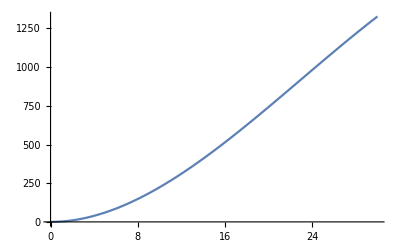

```mathematica
Plot[g[x],{x,0,30}]
```

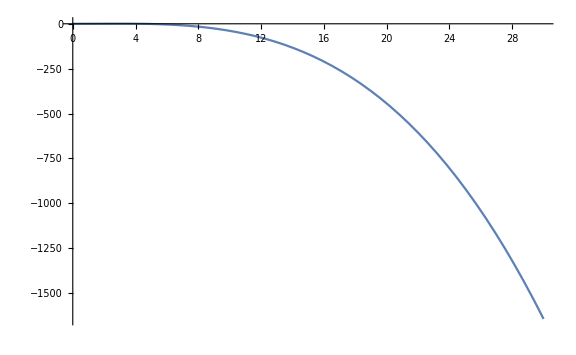

```mathematica
Show[%74,ImageSize->Large]
```

```mathematica
g[x]
```

(1.6 x+(22 (-1+x+√((-1+x)^2+1.6 x)))/14611+(11 (-1+x+√((-1+x)^2+1.6 x))^2)/14611)^2-4 (0.00240914 x (-1+x+√((-1+x)^2+1.6 x))+(22 (-1+x+√((-1+x)^2+1.6 x))^3)/14611)

```mathematica
Solve[(1.6 x+(22 (-1+x+√((-1+x)^2+1.6 x)))/14611+(11 (-1+x+√((-1+x)^2+1.6 x))^2)/14611)^2-4 (0.00240914379577031 x (-1+x+√((-1+x)^2+1.6 x))+(22 (-1+x+√((-1+x)^2+1.6 x))^3)/14611)==0,x]
```

{{x→0.},{x→69.207},{x→4181.64}}